```mathematica
n=16
```

16

```mathematica
dfi=(2π)/n
```

π/8

```mathematica
p1=Table[{-0.49+0.01Cos[π-i dfi],0.01Sin[i dfi]},{i,0,n/4}];
```

```mathematica
p2=Table[{0.49+0.01Cos[π/2-i dfi],0.01Sin[π/2-i dfi]},{i,0,n/4}];
```

```mathematica
p3=Table[{-0.49+0.01Cos[π-i dfi],-0.01Sin[i dfi]},{i,0,n/4}];
```

```mathematica
p4=Table[{0.49+0.01Cos[π/2-i dfi],-0.01Sin[π/2-i dfi]},{i,0,n/4}];
```

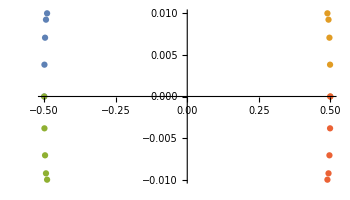

```mathematica
ListPlot[{p1,p2,p3,p4},AspectRatio->Automatic]
```

```mathematica
Join[p1,p2]
```

{{-0.5,0.},{-0.499239,0.00382683},{-0.497071,0.00707107},{-0.493827,0.0092388},{-0.49,0.01},{0.49,0.01},{0.493827,0.0092388},{0.497071,0.00707107},{0.499239,0.00382683},{0.5,0.}}

```mathematica
data=Flatten[{"aaa","bbb",Length[p1]+Length[p2]-1,Length[p3]+Length[p4]-1,"up",Join[p1,p2],"down",Join[p3,p4]},1]
```

{aaa,bbb,9,9,up,{-0.5,0.},{-0.499239,0.00382683},{-0.497071,0.00707107},{-0.493827,0.0092388},{-0.49,0.01},{0.49,0.01},{0.493827,0.0092388},{0.497071,0.00707107},{0.499239,0.00382683},{0.5,0.},down,{-0.5,0.},{-0.499239,-0.00382683},{-0.497071,-0.00707107},{-0.493827,-0.0092388},{-0.49,-0.01},{0.49,-0.01},{0.493827,-0.0092388},{0.497071,-0.00707107},{0.499239,-0.00382683},{0.5,0.}}

```mathematica
p1Rev=Reverse[p1]
```

{{-0.49,0.01},{-0.493827,0.0092388},{-0.497071,0.00707107},{-0.499239,0.00382683},{-0.5,0.}}

```mathematica
p2Rev=Reverse@p2
```

{{0.5,0.},{0.499239,0.00382683},{0.497071,0.00707107},{0.493827,0.0092388},{0.49,0.01}}

```mathematica
p3Rev=Reverse[p3]
```

{{-0.49,-0.01},{-0.493827,-0.0092388},{-0.497071,-0.00707107},{-0.499239,-0.00382683},{-0.5,0.}}

```mathematica
p4Rev=Reverse[p4]
```

{{0.5,0.},{0.499239,-0.00382683},{0.497071,-0.00707107},{0.493827,-0.0092388},{0.49,-0.01}}

```mathematica
dataRev=Flatten[{"aaa","bbb",Length[p1]+Length[p2]-1,Length[p3]+Length[p4]-1,"up",Join[p2Rev,p1Rev],"down",Join[p4Rev,p3Rev]},1]
```

{aaa,bbb,9,9,up,{0.5,0.},{0.499239,0.00382683},{0.497071,0.00707107},{0.493827,0.0092388},{0.49,0.01},{-0.49,0.01},{-0.493827,0.0092388},{-0.497071,0.00707107},{-0.499239,0.00382683},{-0.5,0.},down,{0.5,0.},{0.499239,-0.00382683},{0.497071,-0.00707107},{0.493827,-0.0092388},{0.49,-0.01},{-0.49,-0.01},{-0.493827,-0.0092388},{-0.497071,-0.00707107},{-0.499239,-0.00382683},{-0.5,0.}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Git\VM2D\build\Airfoils\Generators\Blasius

```mathematica
Export["blas200Rev.pfl",dataRev,"Table"]
```

blas200Rev.pfl

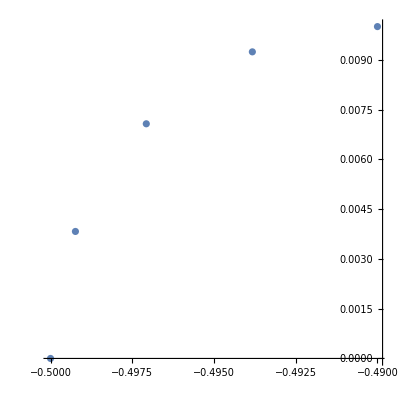

```mathematica
ListPlot[p1,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
Norm[{-0.5,0.}-{-0.49923879532511284,0.003826834323650898}]
```

0.00390181

```mathematica
Norm[{0.5,0.}-{-0.5,0.}]
```

```mathematica
1./0.0039018064403225717
```

256.292